# Linearity

```mathematica
theoreticalColor="TropicalRainForest";
experimentalColor="BrickRed";
zeroFreqColor="Razzmatazz";
zeroFreqColorAtF = "ShamRock";
```

## The relative frequency of 0.

For each virus removal rate value we run a series of experiments and calculate the relative frequency of 0 offsprings.

```mathematica
vrrrangemax=20;
```

```mathematica
theoFreqZeroList={{0.5,19/1000},{2.0,89/1000},{3,114/1000},{4,191/1000},{5,189/1000},{6,212/1000},{8,270/1000},{13,376/1000},{15,421/1000},{16.7, 460/1000},{18,466/1000}};
```

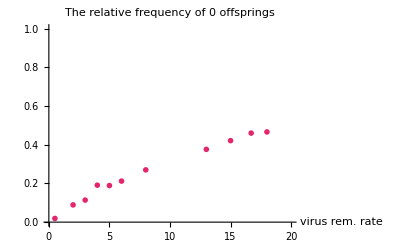

```mathematica
PlotZeroFreq=ListPlot[theoFreqZeroList, 
PlotStyle->{ColorData["Crayola"][zeroFreqColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,vrrrangemax},{0,1}},AxesLabel->{"virus rem. rate",""},PlotLabel->"The relative frequency of 0 offsprings"]
```

This looks similar to part of the 1/(1+(a/x)^n) curve -- Hill equation with n=1:

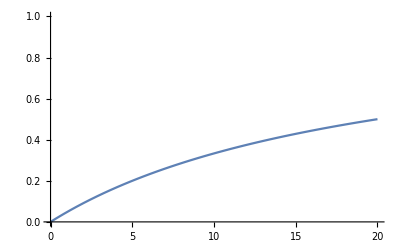

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},PlotRange->{0,1}]
```

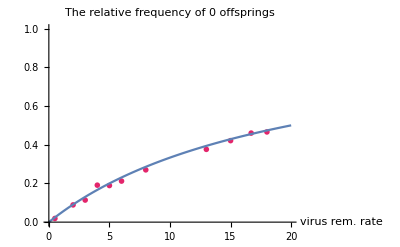

```mathematica
Show[PlotZeroFreq,curvePlot]
```

Observation: the relative frequency of 0 offsprings seems to be described well by 1/(1 + (vrrrangemax/x))

Observation nr2: at this point we have a concave function.

## Offspring distribution

#### Virus removal rate = 3*E-3

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo3.txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,114},{1,121},{2,97},{3,82},{4,93},{5,67},{6,65},{7,40},{8,34},{9,28},{10,28},{11,28},{12,31},{13,25},{14,17},{15,12},{16,18},{17,11},{18,13},{19,12},{20,8},{21,7},{22,10},{23,3},{24,9},{25,3},{26,2},{27,3},{28,2},{29,3},{30,1},{31,1},{32,0},{33,1},{34,3},{35,2},{36,1},{37,0},{38,3},{39,0},{40,0},{41,0},{42,0},{43,1},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,1}}

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=3*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr.(freq zero)"];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

Gábor ötlete: geom param: mintaátlag reciproka, ML becslés; K-S próba.
Végeredmény: melyik param becslés ad jobb illeszkedést.

```mathematica
geohope=1/(Mean[cleanData]+1)
```

0.128617

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geohope],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

#### Virus removal rate = 13*E-3

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo13.txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,376},{1,248},{2,142},{3,105},{4,53},{5,31},{6,19},{7,6},{8,9},{9,7},{10,3},{11,1}}

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=13*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr.(freq zero)"];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
probabilityData[[1,2]]/1000 //N
```

0.376

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

Gábor ötlete: geom param: mintaátlag reciproka, ML becslés; K-S próba.
Végeredmény: melyik param becslés ad jobb illeszkedést.

```mathematica
geohope=1/(Mean[cleanData]+1)
```

0.392773

```mathematica
Max[cleanData]
```

11.

```mathematica
geohope
```

0.392773

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geohope],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

## Branching processes: the theoretical PoE

Using the above observation regarding a reasonable fit to geometrical distribution, the PoE is given by the fix point of the PGF of the geometrical distribution.

The POE is given by

G_X(q)=q
q / (1 - (1-q)x) = x, thus we have
q = x * (1 - (1-q)x) 

We have a simple second order equation. The non-negative solution to that is:

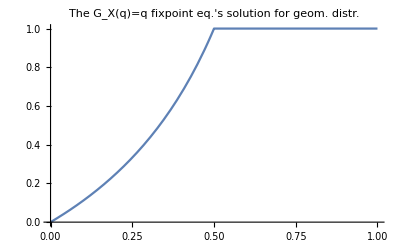

```mathematica
Plot[N[(1-Sqrt[1-4*(1-(q))*(q)])/(2*(1-(q)))],{q,0,1},PlotLabel->"The G_X(q)=q fixpoint eq.'s solution for geom. distr."]
```

We have seen that q = q(mu), where we found that q = q(mu) takes the following form: q(mu) = 1 / (1 + 20/mu)

Altogether we have

q / (1 - (1-q)x) = x and
q(mu) = 1 / (1 + 20/mu)

The probability of extinction is given (below on the LHS) as a function of q (the relative frequency of 0 offsprings), and for that to be a linear function of mu we need the following:

```mathematica
Solve[(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))==(1/20)*mu,q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{q→mu/(20+mu)}}

Which corresponds to what we have previously observed.

## Comparing results

### Expectation

```mathematica
PoE[q_]:=(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))
```

```mathematica
relFreq[mu_]:=1/(1 + 20/mu)
```

```mathematica
theoFreqZeroListAtF={{0.5,PoE[relFreq[0.5]]},{2.0,PoE[relFreq[2.0]]},{3,PoE[relFreq[3.0]]},{4,PoE[relFreq[4.0]]},{5,PoE[relFreq[5]]},{6,PoE[relFreq[6]]},{8,PoE[relFreq[8]]},{13,PoE[relFreq[13]]},{15,PoE[relFreq[15]]},{16.7, PoE[relFreq[16.7]]},{18,PoE[relFreq[18]]}};
```

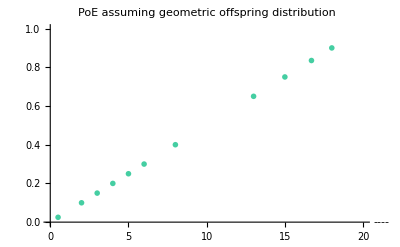

```mathematica
PlotZeroFreqAtF=ListPlot[theoFreqZeroListAtF, 
PlotStyle->{ColorData["Crayola"][zeroFreqColorAtF],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,20},{0,1}},AxesLabel->{"----",""},PlotLabel->"PoE assuming geometric offspring distribution"]
```

### Observation

```mathematica
theoList={{0.5,0.0403},{1.67, 0.074},{2.0,0.0973},{3,0.1318},{4,0.227592},{5,0.24502},{6,0.2687},{8,0.36},{13,0.624},{15,0.78},{16.7, 0.8714},{18,0.904}}
```

{{0.5,0.0403},{1.67,0.074},{2.,0.0973},{3,0.1318},{4,0.227592},{5,0.24502},{6,0.2687},{8,0.36},{13,0.624},{15,0.78},{16.7,0.8714},{18,0.904}}

```mathematica
experimentalList={{0.5,23/1000},{1.67, 78/1000},{2,95/1000 },{6,288/1000},{8,391/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{16.7, 893/1000}}
```

{{0.5,23/1000},{1.67,39/500},{2,19/200},{6,36/125},{8,391/1000},{10,469/1000},{11,559/1000},{12,301/500},{13,637/1000},{16.7,893/1000}}

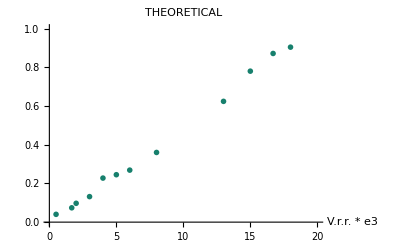

```mathematica
PlotTheoretical=ListPlot[theoList, 
PlotStyle->{ColorData["Crayola"][theoreticalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,20},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"THEORETICAL"]
```

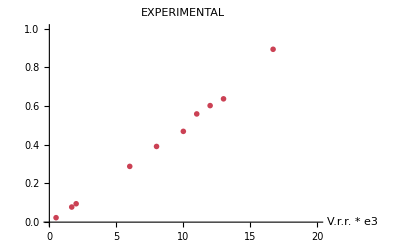

```mathematica
PlotExperimental=ListPlot[experimentalList, 
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},PlotRange->{{0,20},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"EXPERIMENTAL"]
```

Todo: futtatások, empirikus megfigyelés a 0.5 fölötti részre.